# Taylor Modeling

## Jonathan Pincince

## Mathematica 1: Linear Approximations

Two straightforward trig functions plotted along with their derivatives, and the linear approximations of a local neighborhood using the first derivative at a point.

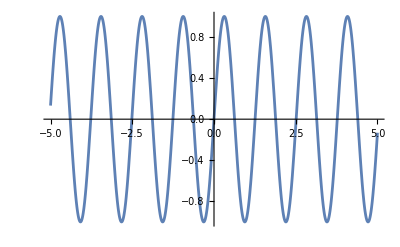

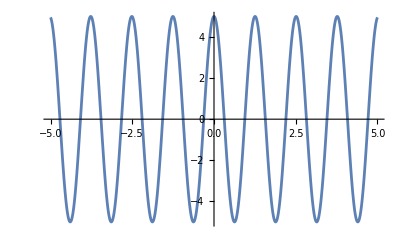

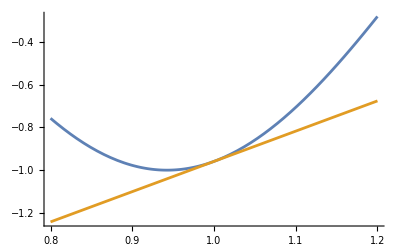

```mathematica
f[x_] := Sin[5x];
Plot[f[x], {x, -5, 5}]
Plot[f'[x], {x, -5, 5}]
x0 = 1;
lf[x_] := f[x0] + f'[x0]*(x-x0);
Plot[{f[x], lf[x]}, {x, 0.8, 1.2}]
```

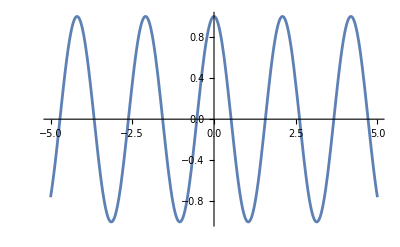

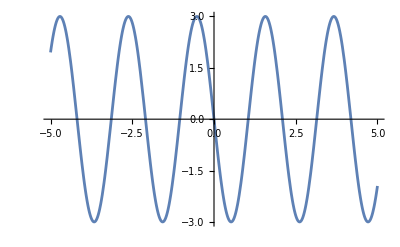

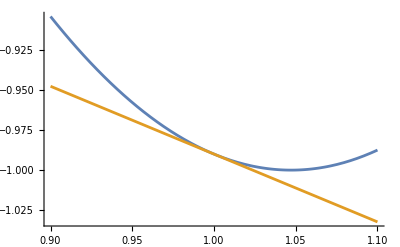

```mathematica
g[x_] := Cos[3x];
Plot[g[x], {x, -5, 5}]
Plot[g'[x], {x, -5, 5}]
x0 = 1;
lg[x_] := g[x0] + g'[x0]*(x-x0);
Plot[{g[x], lg[x]}, {x, 0.9, 1.1}]
```

### Testing of Linear Approximation

Defining the four functions for testing:

```mathematica
f1[x_] := Cos[((x^5)-1) / (1 + x^3)]
f2[x_] := Cos[x * ( (1-Cos[2x]) / (2 + Sin[x])^2 )]
f3[x_] := Cos[x * ( (1-Cos[2x]) / (1 + Sin[x])^2 )]
f4[x_] := Cos[x * Sin[1/x]]
```

Plot f1, its derivative, and the linear approximation superimposed on f1. The first linear approximation is shown in a neighborhood where the graph and its derivative look relatively linear, but the second approximation (in area of problematic derivative) clearly looks worse; even at a smaller scale, the linear approximation deviates rapidly.

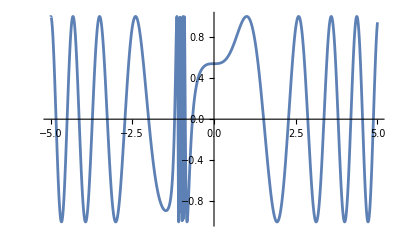

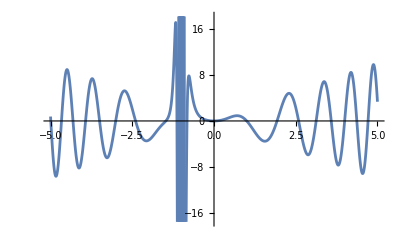

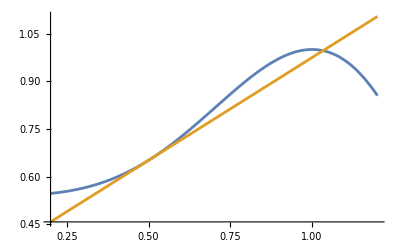

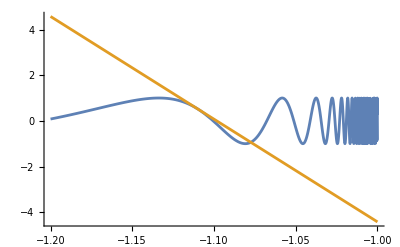

```mathematica
Plot[f1[x], {x, -5, 5}]
Plot[f1'[x], {x, -5, 5}]
x0 = 0.5;
x1 = -1.11;
lf1[x_] := f1[x0] + f1'[x0]*(x-x0);
l2f1[x_] := f1[x1] + f1'[x1]*(x-x1);
Plot[{f1[x], lf1[x]}, {x, 0.2, 1.2}]
Plot[{f1[x], l2f1[x]}, {x, -1.2, -1}]
```

Plot f2, its derivative, and the linear approximation superimposed on the function. The linear fit is decent in a small enough neighborhood since the neighborhood’s derivative looks linear.

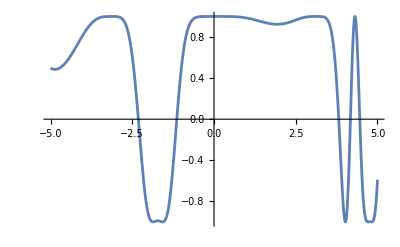

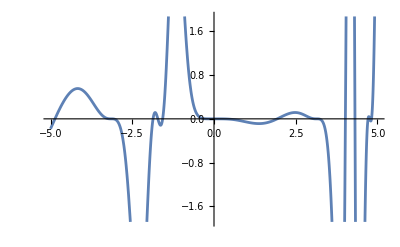

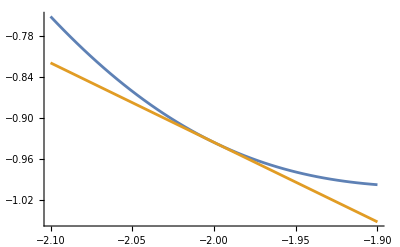

```mathematica
Plot[f2[x], {x, -5, 5}]
Plot[f2'[x], {x, -5, 5}]
x0 = -2;
lf2[x_] := f2[x0] + f2'[x0]*(x-x0);
Plot[{f2[x], lf2[x]}, {x, -2.1, -1.9}]
```

Plot f3, its derivative, and the linear approximation superimposed on the function. Again by choosing the right neighborhood, the linear approximation can be made to look good, but if you tried to make this work in the chaotic area between about -2.5 and -1, the approximation would again be poor, like with the first test function.

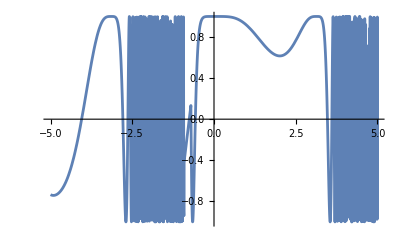

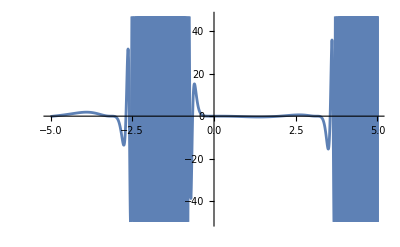

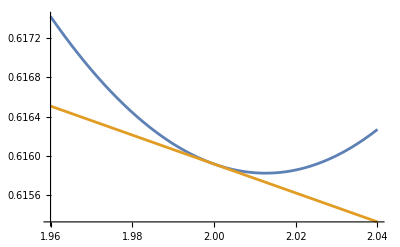

```mathematica
Plot[f3[x], {x, -5, 5}]
Plot[f3'[x], {x, -5, 5}]
x0 = 2;
lf3[x_] := f3[x0] + f3'[x0]*(x-x0);
Plot[{f3[x], lf3[x]}, {x, 1.96, 2.04}]
```

Plot f4, its derivative, and the linear approximation superimposed on the function. Again in linear looking neighborhoods, the approximation does well, but we can see from the graph of the derivative that we’ll have issues in the neighborhood around x = 0, and this comes true in the final graph.

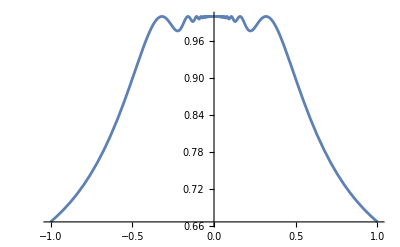

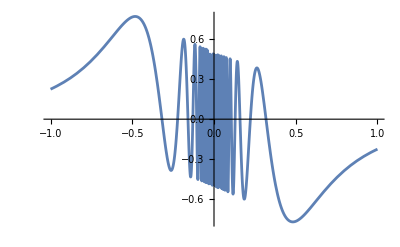

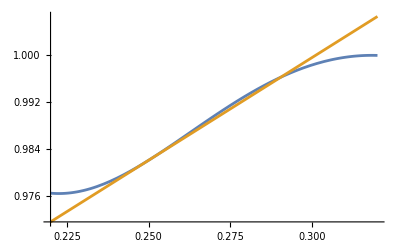

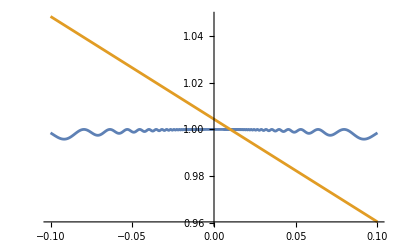

```mathematica
Plot[f4[x], {x, -1, 1}]
Plot[f4'[x], {x, -1, 1}]
x0 = 0.25;
x1 = 0.01;
lf4[x_] := f4[x0] + f4'[x0]*(x-x0);
l2f4[x_] := f4[x1] + f4'[x1]*(x-x1);
Plot[{f4[x], lf4[x]}, {x, 0.22, 0.32}]
Plot[{f4[x], l2f4[x]}, {x, -0.1, 0.1}]
```

## Mathematica 2: Verifying Taylor-Lagrange

The below graph shows that there must be a ‘c’ between (a, b) which satisfies the Taylor-Lagrange formula. The formula t(x) defined below is TL with a = 1, b = 3, and we can see that there is a value of c between these two which makes the function equal to zero, near c = 1.625. The ‘difference’ term (between f(a) and f(b)) is everything past fa-fb, since some rearranging of the formula could put fb - fa on the left hand side. Therefore in order to find their difference, we need a ‘c’ which makes the entire formula equal to zero, or in the rearranged case, makes fb-fa equal to the ‘difference’ term.

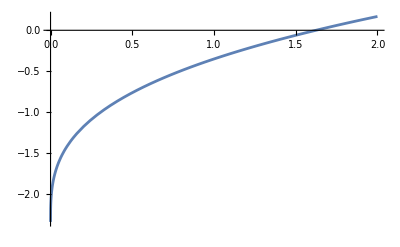

```mathematica
f[x_]:=(9/28)(x^(7/3))
fa:=f[1];
fb:=f[3];
t[c_]:=fa-fb+((3-1)f'[1])+((1/2)((3-1)^2)(f''[c]));
plotF=Plot[t[c],{c,0,2}]
```

## Mathematica 3: Error in Linear Approximation

To see the errors involved in the linear approximation f'(x)= for some small h, below I’ve taken one of the example functions I used in part 1, and created an approximation. The actual and approximate derivatives are found at x=2 and tested for a few values of h.

Approximate derivatives at x = 2 with the h value used in approximation

{{0.1,-0.137386},{0.2,-0.131555},{0.3,-0.126232},{0.4,-0.121354},{0.5,-0.116869},{0.6,-0.11273},{0.7,-0.108899},{0.8,-0.105344},{0.9,-0.102035},{1.,-0.0989483}}

Actual derivative at x = 2 (h value present but not relevant)

{{0.1,-0.143803},{0.2,-0.143803},{0.3,-0.143803},{0.4,-0.143803},{0.5,-0.143803},{0.6,-0.143803},{0.7,-0.143803},{0.8,-0.143803},{0.9,-0.143803},{1.,-0.143803}}

Absolute errors with the corresponding h value

{{0.1,-0.00641689},{0.2,-0.0122486},{0.3,-0.0175715},{0.4,-0.022449},{0.5,-0.0269346},{0.6,-0.0310735},{0.7,-0.0349042},{0.8,-0.0384596},{0.9,-0.0417683},{1.,-0.0448548}}

Relative errors as percentages printed next to the h value that produced them; this is where it's easy to see that a large h produces larger errors. The effect may be outsized since h is on the same order of magnitude as x, but it does illustrate the point.

{{0.1,4.67069},{0.2,9.31067},{0.3,13.92},{0.4,18.4987},{0.5,23.0469},{0.6,27.5647},{0.7,32.0519},{0.8,36.5088},{0.9,40.9353},{1.,45.3315}}

Actual derivative values in red, approximations in blue. You can see the approximations drift further and further from reality as h grows

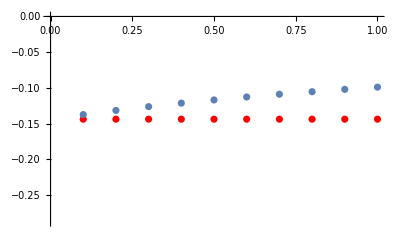

```mathematica
m[x_]:=Cos[(0.01x^2)+1]/x;
MDApprox[x_,h_]:=(m[x+h]-m[x])/h;
MDActual[x_]:=m'[x];

ActualDerivs={};
ApproxDerivs={};
ActualErrs={};
RelativeErrs={};

For[k=1,k<=10,k++,
h=k*0.1;
approx1:=MDApprox[2,h];
actual1:=MDActual[2];
ActualDerivs=Append[ActualDerivs,{h,actual1}];
ApproxDerivs=Append[ApproxDerivs,{h,approx1}];
ActualErr=actual1-approx1;
RelativeErr=((actual1-approx1)/approx1)*100;
ActualErrs=Append[ActualErrs,{h,ActualErr}];
RelativeErrs=Append[RelativeErrs,{h,RelativeErr}];
]
Print["Approximate derivatives at x = 2 with the h value used in approximation"]
ApproxDerivs
Print["Actual derivative at x = 2 (h value present but not relevant)"]
ActualDerivs
Print["Absolute errors with the corresponding h value"]
ActualErrs
Print["Relative errors as percentages printed next to the h value that produced them; this is where it's easy to see that a large h produces larger errors. The effect may be outsized since h is on the same order of magnitude as x, but it does illustrate the point."]
RelativeErrs

plotMDActual=ListPlot[ActualDerivs,PlotStyle->Red];
plotMDApprox=ListPlot[ApproxDerivs];
Print["Actual derivative values in red, approximations in blue. You can see the approximations drift further and further from reality as h grows"]
Show[{plotMDActual, plotMDApprox}]
```

## Mathematica 4: Improved Error in Linear Approximation

This section uses the improvement on the linear approximation in order to find the derivative of the function at a point. In order to illustrate the improved error, I’ve used the same function m[x], and defined MDApprox2 as the more precise formula. Then the rest of the work is essentially the same, only difference being in the outputs.

Improved approximate derivatives at x = 2 with the h value used in approximation. Can see that these are different from the original approximation

{{0.1,-0.144142},{0.2,-0.145168},{0.3,-0.146914},{0.4,-0.149435},{0.5,-0.152813},{0.6,-0.15717},{0.7,-0.16267},{0.8,-0.169545},{0.9,-0.178118},{1.,-0.188849}}

Actual derivative at x = 2 (h value present but not relevant)

{{0.1,-0.143803},{0.2,-0.143803},{0.3,-0.143803},{0.4,-0.143803},{0.5,-0.143803},{0.6,-0.143803},{0.7,-0.143803},{0.8,-0.143803},{0.9,-0.143803},{1.,-0.143803}}

Absolute errors with the corresponding h value

{{0.1,0.000338748},{0.2,0.00136525},{0.3,0.00311107},{0.4,0.00563155},{0.5,0.00901035},{0.6,0.0133668},{0.7,0.0188671},{0.8,0.0257422},{0.9,0.0343153},{1.,0.0450463}}

Relative errors as percentages printed next to the h value that produced them; this is where it's easy to see that a large h produces larger errors. The effect may be outsized since h is on the same order of magnitude as x, but it does illustrate the point.

{{0.1,-0.23501},{0.2,-0.94046},{0.3,-2.11761},{0.4,-3.76857},{0.5,-5.8963},{0.6,-8.50466},{0.7,-11.5984},{0.8,-15.1831},{0.9,-19.2654},{1.,-23.853}}

Actual derivative values in red, approximations in blue. You can see the approximations drift further and further from reality as h grows, but you can also see that as h shrinks, the approximation improves at a quadratic rate and is nearly nothing for the smallest h.

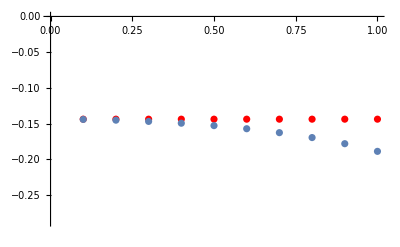

```mathematica
MDApprox2[x_,h_]:=((m[x+h]-m[x-h])/(2*h));

ActualDerivs2={};
ApproxDerivs2={};
ActualErrs2={};
RelativeErrs2={};

For[k=1,k<=10,k++,
h=k*0.1;
approx2:=MDApprox2[2,h];
actual2:=MDActual[2];
ActualDerivs2=Append[ActualDerivs2,{h,actual2}];
ApproxDerivs2=Append[ApproxDerivs2,{h,approx2}];
ActualErr2=actual2-approx2;
RelativeErr2=((actual2-approx2)/approx2)*100;
ActualErrs2=Append[ActualErrs2,{h,ActualErr2}];
RelativeErrs2=Append[RelativeErrs2,{h,RelativeErr2}];
]
Print["Improved approximate derivatives at x = 2 with the h value used in approximation. Can see that these are different from the original approximation"]
ApproxDerivs2
Print["Actual derivative at x = 2 (h value present but not relevant)"]
ActualDerivs2
Print["Absolute errors with the corresponding h value"]
ActualErrs2
Print["Relative errors as percentages printed next to the h value that produced them; this is where it's easy to see that a large h produces larger errors. The effect may be outsized since h is on the same order of magnitude as x, but it does illustrate the point."]
RelativeErrs2

plotMDActual2=ListPlot[ActualDerivs2,PlotStyle->Red];
plotMDApprox2=ListPlot[ApproxDerivs2];
Print["Actual derivative values in red, approximations in blue. You can see the approximations drift further and further from reality as h grows, but you can also see that as h shrinks, the approximation improves at a quadratic rate and is nearly nothing for the smallest h."]
Show[{plotMDActual2, plotMDApprox2}]
```